# Data Analysis: Autosomal

## Data Pre - Processing

Load

Setup folders, and return CSV filenames in the experiments sub-folder.

```mathematica
SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/ProcessedData"];
experimentsFolder="/Autosomal/";
fileNames=FileNames["*.csv",Directory[]<>experimentsFolder];
```

Import the data from the files, flatten it into a large dataset, and store the headers.

```mathematica
header=Import[fileNames[[1]]][[1]];
rawData=(Import[#][[2;;All]])&/@fileNames;
flattenedData=ToExpression/@Flatten[rawData,1];
```

Show summaries.

```mathematica
{header,Range[header//Length]}//Transpose//Grid[#,Frame->All]&
experimentsIDVectors=Cases[flattenedData,{homing_,femaleDep_,hFitness_,bFitness_,___}->{homing,femaleDep,hFitness,bFitness}];
Grid[{
header[[1;;4]],
(experimentsIDVectors[[All,#]]//DeleteDuplicates//Sort)&/@Range[4]
}//Transpose,Frame->All
]
```

Homing | 1
FemaleDeposition | 2
HFitness | 3
BFitness | 4
Day | 5
H | 6
W | 7
R | 8
B | 9

Homing | {0.65,0.7,0.75,0.8,0.9,0.95,0.99}
FemaleDeposition | {0.,0.25,0.5,0.75}
HFitness | {0.,0.02,0.04,0.06,0.08,0.1}
BFitness | {0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4}

Pre - Process

Calculate the "max" number of days, and pop sizes in case these are useful for sampling and re-scaling the output.

```mathematica
maxDay=flattenedData[[All,5]]//Max;
maxTotalPop=Max[Total/@flattenedData[[All,6;;9]]];
maxAllelePop=Max[Max/@flattenedData[[All,6;;9]]];
```

```mathematica
reShapedData={
#[[1]],#[[2]],#[[3]],#[[4]],
#[[5]]//Round,
#[[6]]/maxTotalPop,
#[[7]]/maxTotalPop,
#[[8]]/maxTotalPop,
#[[9]]/maxTotalPop
}&/@flattenedData;
```

```mathematica
dayProbed=999;
probedData=Cases[reShapedData,{homing_,femaleDep_,hFitness_,bFitness_,dayProbed,h_,w_,r_,b_}->{homing,femaleDep,hFitness,bFitness,h/(h+w+r+b)}];
```

## Analyze

Reshape into I/O

```mathematica
outInDataForm=(#[[5]]->{#[[1]],#[[2]],#[[3]],#[[4]]})&/@probedData;
inOutDataForm=({#[[1]],#[[2]],#[[3]],#[[4]]}->#[[5]])&/@probedData;
```

Find Clusters (Exploratory)

```mathematica
clusters=FindClusters[inOutDataForm];
Length[clusters]
```

6

{{0.65,0.25,0.,0.05,0.688212},{0.65,0.25,0.,0.1,0.787077},{0.65,0.25,0.,0.15,0.832024},{0.65,0.25,0.,0.2,0.876609},{0.65,0.5,0.,0.05,0.575573},{0.65,0.5,0.,0.1,0.68952},{0.65,0.5,0.,0.15,0.786418},{0.65,0.5,0.,0.2,0.813269},{0.65,0.5,0.,0.25,0.832259},{0.65,0.5,0.,0.3,0.858647},{0.65,0.5,0.,0.35,0.875602},{0.65,0.5,0.,0.4,0.873767},{0.65,0.5,0.02,0.05,0.510134},{0.65,0.5,0.02,0.1,0.611278},{0.65,0.5,0.02,0.15,0.67542},{0.65,0.5,0.02,0.2,0.778784},{0.65,0.5,0.02,0.25,0.808292},{0.65,0.5,0.02,0.3,0.802286},{0.65,0.5,0.02,0.35,0.815642},{0.65,0.5,0.02,0.4,0.826817},{0.65,0.5,0.04,0.05,0.434181},{0.65,0.5,0.04,0.1,0.531708},{0.65,0.5,0.04,0.15,0.63752},{0.65,0.5,0.04,0.2,0.706303},{0.65,0.5,0.04,0.25,0.703269},{0.65,0.5,0.04,0.3,0.743},{0.65,0.5,0.04,0.35,0.728902},{0.65,0.5,0.04,0.4,0.742018},{0.65,0.75,0.,0.05,0.451898},{0.65,0.75,0.,0.1,0.572622},{0.65,0.75,0.,0.15,0.674158},{0.65,0.75,0.,0.2,0.673132},{0.65,0.75,0.,0.25,0.703078},{0.65,0.75,0.,0.3,0.755097},{0.65,0.75,0.,0.35,0.698684},{0.65,0.75,0.,0.4,0.734365},{0.65,0.75,0.02,0.05,0.392992},{0.65,0.75,0.02,0.1,0.464963},{0.65,0.75,0.02,0.15,0.564975},{0.65,0.75,0.02,0.2,0.560119},{0.65,0.75,0.02,0.25,0.675205},{0.65,0.75,0.02,0.3,0.644029},{0.65,0.75,0.02,0.35,0.679583},{0.65,0.75,0.02,0.4,0.642563},{0.65,0.75,0.04,0.05,0.30032},{0.65,0.75,0.04,0.1,0.3953},{0.65,0.75,0.04,0.15,0.449997},{0.65,0.75,0.04,0.2,0.521876},{0.65,0.75,0.04,0.25,0.543759},{0.65,0.75,0.04,0.3,0.549727},{0.65,0.75,0.04,0.35,0.542813},{0.65,0.75,0.04,0.4,0.577401},{0.7,0.25,0.,0.05,0.744946},{0.7,0.25,0.,0.1,0.826993},{0.7,0.25,0.,0.15,0.867494},{0.7,0.5,0.,0.05,0.641033},{0.7,0.5,0.,0.1,0.745249},{0.7,0.5,0.,0.15,0.823859},{0.7,0.5,0.,0.2,0.857035},{0.7,0.5,0.,0.25,0.884834},{0.7,0.5,0.,0.3,0.886152},{0.7,0.5,0.,0.35,0.892938},{0.7,0.5,0.,0.4,0.893428},{0.7,0.5,0.02,0.05,0.552913},{0.7,0.5,0.02,0.1,0.686718},{0.7,0.5,0.02,0.15,0.765151},{0.7,0.5,0.02,0.2,0.794735},{0.7,0.5,0.02,0.25,0.848919},{0.7,0.5,0.02,0.3,0.830223},{0.7,0.5,0.02,0.35,0.862329},{0.7,0.5,0.02,0.4,0.85602},{0.7,0.5,0.04,0.05,0.483136},{0.7,0.5,0.04,0.1,0.594443},{0.7,0.5,0.04,0.15,0.681541},{0.7,0.5,0.04,0.2,0.755995},{0.7,0.5,0.04,0.25,0.771379},{0.7,0.5,0.04,0.3,0.770462},{0.7,0.5,0.04,0.35,0.7867},{0.7,0.5,0.04,0.4,0.828527},{0.7,0.75,0.,0.05,0.495706},{0.7,0.75,0.,0.1,0.629335},{0.7,0.75,0.,0.15,0.705841},{0.7,0.75,0.,0.2,0.765936},{0.7,0.75,0.,0.25,0.768766},{0.7,0.75,0.,0.3,0.795682},{0.7,0.75,0.,0.35,0.785429},{0.7,0.75,0.,0.4,0.835917},{0.7,0.75,0.02,0.05,0.400402},{0.7,0.75,0.02,0.1,0.54062},{0.7,0.75,0.02,0.15,0.614324},{0.7,0.75,0.02,0.2,0.662285},{0.7,0.75,0.02,0.25,0.684279},{0.7,0.75,0.02,0.3,0.736301},{0.7,0.75,0.02,0.35,0.686537},{0.7,0.75,0.02,0.4,0.678632},{0.7,0.75,0.04,0.05,0.356412},{0.7,0.75,0.04,0.1,0.454586},{0.7,0.75,0.04,0.15,0.545955},{0.7,0.75,0.04,0.2,0.596526},{0.7,0.75,0.04,0.25,0.590016},{0.7,0.75,0.04,0.3,0.648242},{0.7,0.75,0.04,0.35,0.5894},{0.7,0.75,0.04,0.4,0.637155},{0.75,0.25,0.,0.05,0.760835},{0.75,0.25,0.,0.1,0.860032},{0.75,0.25,0.,0.15,0.899872},{0.75,0.5,0.,0.05,0.651456},{0.75,0.5,0.,0.1,0.771829},{0.75,0.5,0.,0.15,0.84667},{0.75,0.5,0.,0.2,0.868781},{0.75,0.5,0.,0.25,0.882585},{0.75,0.5,0.,0.3,0.923777},{0.75,0.5,0.,0.35,0.890245},{0.75,0.5,0.,0.4,0.909385},{0.75,0.5,0.02,0.05,0.576571},{0.75,0.5,0.02,0.1,0.717615},{0.75,0.5,0.02,0.15,0.765474},{0.75,0.5,0.02,0.2,0.831004},{0.75,0.5,0.02,0.25,0.868121},{0.75,0.5,0.02,0.3,0.855404},{0.75,0.5,0.02,0.35,0.874138},{0.75,0.5,0.02,0.4,0.90159},{0.75,0.5,0.04,0.05,0.51576},{0.75,0.5,0.04,0.1,0.642054},{0.75,0.5,0.04,0.15,0.747127},{0.75,0.5,0.04,0.2,0.787389},{0.75,0.5,0.04,0.25,0.845549},{0.75,0.5,0.04,0.3,0.836205},{0.75,0.5,0.04,0.35,0.864024},{0.75,0.5,0.04,0.4,0.813179},{0.75,0.75,0.,0.05,0.517364},{0.75,0.75,0.,0.1,0.65857},{0.75,0.75,0.,0.15,0.733367},{0.75,0.75,0.,0.2,0.775551},{0.75,0.75,0.,0.25,0.819388},{0.75,0.75,0.,0.3,0.816079},{0.75,0.75,0.,0.35,0.79066},{0.75,0.75,0.,0.4,0.83517},{0.75,0.75,0.02,0.05,0.460352},{0.75,0.75,0.02,0.1,0.562087},{0.75,0.75,0.02,0.15,0.686157},{0.75,0.75,0.02,0.2,0.730069},{0.75,0.75,0.02,0.25,0.719806},{0.75,0.75,0.02,0.3,0.764192},{0.75,0.75,0.02,0.35,0.769426},{0.75,0.75,0.02,0.4,0.77117},{0.75,0.75,0.04,0.05,0.401905},{0.75,0.75,0.04,0.1,0.515408},{0.75,0.75,0.04,0.15,0.611949},{0.75,0.75,0.04,0.2,0.629766},{0.75,0.75,0.04,0.25,0.664118},{0.75,0.75,0.04,0.3,0.713009},{0.75,0.75,0.04,0.35,0.681543},{0.75,0.75,0.04,0.4,0.728325},{0.8,0.25,0.,0.05,0.811181},{0.8,0.25,0.,0.1,0.88395},{0.8,0.5,0.,0.05,0.692032},{0.8,0.5,0.,0.1,0.814498},{0.8,0.5,0.,0.15,0.853334},{0.8,0.5,0.,0.2,0.89592},{0.8,0.5,0.,0.25,0.919881},{0.8,0.5,0.,0.3,0.907935},{0.8,0.5,0.,0.35,0.941051},{0.8,0.5,0.,0.4,0.912089},{0.8,0.5,0.02,0.05,0.633017},{0.8,0.5,0.02,0.1,0.751328},{0.8,0.5,0.02,0.15,0.84532},{0.8,0.5,0.02,0.2,0.863728},{0.8,0.5,0.02,0.25,0.890562},{0.8,0.5,0.02,0.3,0.869723},{0.8,0.5,0.02,0.35,0.900213},{0.8,0.5,0.04,0.15,0.794278},{0.8,0.5,0.04,0.2,0.826915},{0.8,0.5,0.04,0.25,0.860244},{0.8,0.5,0.04,0.3,0.865721},{0.8,0.75,0.,0.05,0.573135},{0.8,0.75,0.,0.1,0.724789},{0.8,0.75,0.,0.15,0.733146},{0.8,0.75,0.,0.2,0.850419},{0.8,0.75,0.,0.25,0.845511},{0.8,0.75,0.,0.3,0.857568},{0.8,0.75,0.,0.35,0.870773},{0.8,0.75,0.,0.4,0.895196},{0.8,0.75,0.02,0.05,0.472519},{0.8,0.75,0.02,0.1,0.634885},{0.8,0.75,0.02,0.15,0.714085},{0.8,0.75,0.02,0.2,0.751295},{0.8,0.75,0.02,0.25,0.797613},{0.8,0.75,0.02,0.3,0.789247},{0.8,0.75,0.02,0.35,0.760134},{0.8,0.75,0.04,0.1,0.519543},{0.8,0.75,0.04,0.15,0.642396},{0.8,0.75,0.04,0.2,0.732903},{0.8,0.75,0.04,0.25,0.737887},{0.8,0.75,0.04,0.3,0.768989},{0.9,0.75,0.,0.25,0.894991}}

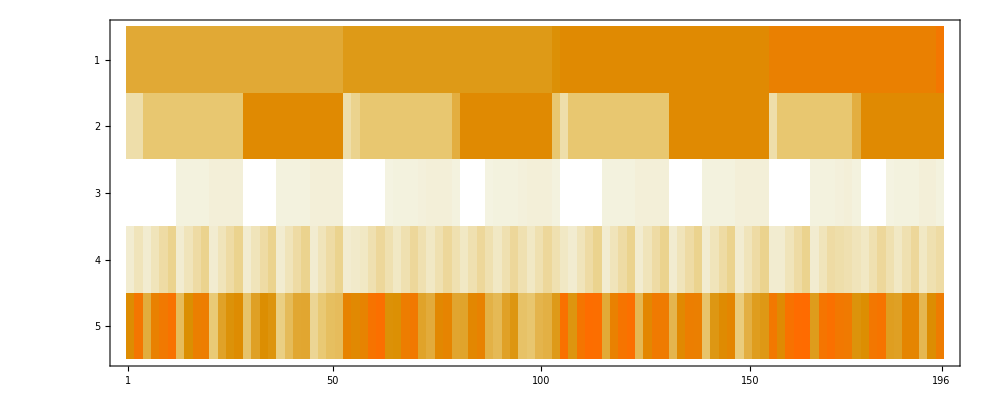

```mathematica
clusterToInspect=2;
clusteredData=Flatten[Cases[outInDataForm,(#->a_)->{a,#}]&/@clusters[[clusterToInspect]],1];
Flatten/@clusteredData
MatrixPlot[%//Transpose,ImageSize->1000]
```

Machine Learning (Predictive)

## One - Fold

Setting up training and validation sets

```mathematica
validationFraction=.9;
samplesNumber=(inOutDataForm//Length);
trainingIndex=samplesNumber*validationFraction//Round;

sample=RandomSample[inOutDataForm];
training=sample[[1;;trainingIndex]];
validation=sample[[(trainingIndex+1);;samplesNumber]];
```

Training and testing

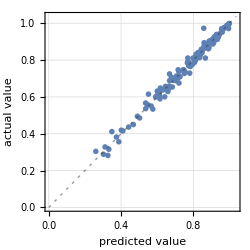
Predictor information
Input type | NumericalVector (length: 4)
Method | GradientBoostedTrees
Standard deviation | 0.0401 ± 0.0066
Loss | 0 ± 0.095
Single evaluation time | 2.89 ms/example
Batch evaluation speed | 71.9 examples/ms
Predictor memory | 685. kB
Training examples used | 1210 examples
Training time | 8.52 s
 |  | Predictor Measurements
Number of test examples | 134
Standard deviation | 0.0222 ± 0.0026
Standard deviation baseline | 0.176 ± 0.011
Mean cross entropy | -2.31 ± 0.19
Single evaluation time | 2.95 ms/example
Batch evaluation speed | 1.51 examples/ms
-Graphics- |

```mathematica
predictionFunction=Predict[training
,ValidationSet->validation
,PerformanceGoal->"Quality"
,Method->"GradientBoostedTrees"
];
Grid[{{
PredictorInformation[predictionFunction],
PredictorMeasurements[predictionFunction,validation, "Report"]
}}]
```

## Repeated random sub-sampling validation

```mathematica
{trainingFraction,folds}={.8,20};
samplesNumber=(inOutDataForm//Length);
trainingIndex=(samplesNumber*trainingFraction)//Round;
trainPlots=Table[
(*Pull a random sample of training/validation sets*)
sample=RandomSample[inOutDataForm];
training=sample[[1;;trainingIndex]];
validation=sample[[(trainingIndex+1);;samplesNumber]];
(*Train the model*)
predictionFunction=Predict[training
,Method->"GradientBoostedTrees"
,PerformanceGoal->"Quality"
,TrainingProgressReporting->"SimplePanel"
,ValidationSet->validation
];
(*Get summary statistics*)
PredictorMeasurements[predictionFunction,validation,"ComparisonPlot"]
,{i,1,folds}];
```

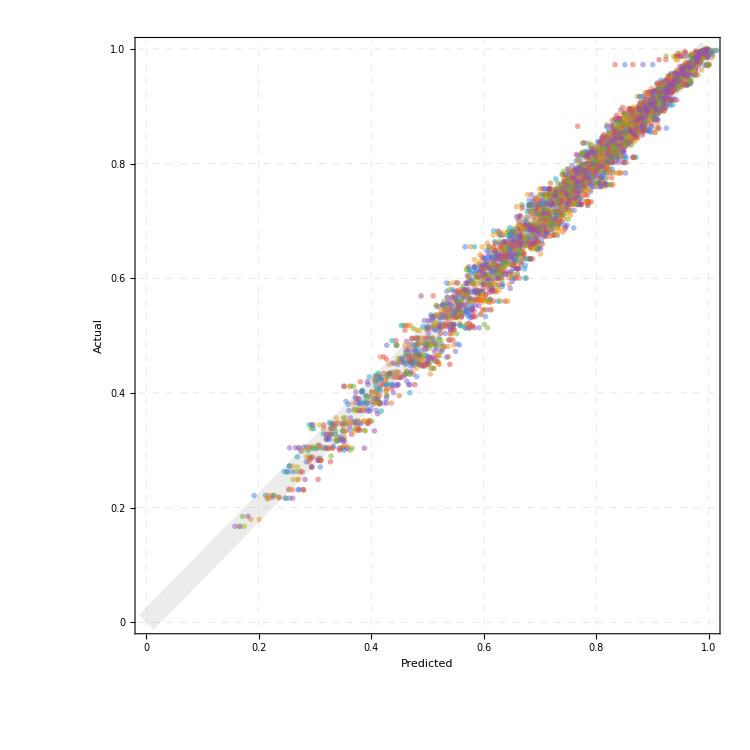

```mathematica
comparisonsPoints=Table[Flatten[trainPlots[[i,1,1,1,1,2,1,1,2,2]],1],{i,1,folds}];
ListPlot[comparisonsPoints
,AspectRatio->1
,Epilog->{Gray,Opacity[.15],Thickness[.02],Line[{{0,0},{1,1}}]}
,Frame->True
,FrameLabel->(Style[#,40]&/@{"Predicted","Actual"})
,FrameStyle->Directive[Gray,Thick]
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.25],Dashed,Thick]
,ImageSize->750
,PlotRange->{{0,1},{0,1}}
,PlotTheme->"Business"
,PlotStyle->Directive[Opacity[.5]]
]
```

Sensitivity Analysis

## Dropping Variables

```mathematica
pickedVariables={1,2,3,4};
{trainingPicked,validationPicked}=Table[
(#[[1]]->#[[2]])&/@Transpose[{
Transpose[i[[All,1,#]]&/@pickedVariables],
i[[All,2]]
}]
,{i,{training,validation}}];
```

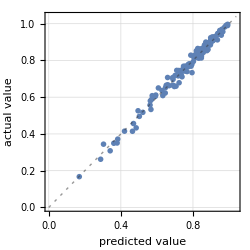
Predictor information
Input type | NumericalVector (length: 4)
Method | GradientBoostedTrees
Standard deviation | 0.038 ± 0.0072
Loss | 0 ± 0.095
Single evaluation time | 2.85 ms/example
Batch evaluation speed | 65.3 examples/ms
Predictor memory | 720. kB
Training examples used | 1210 examples
Training time | 8.36 s
 |  | Predictor Measurements
Number of test examples | 134
Standard deviation | 0.0197 ± 0.0014
Standard deviation baseline | 0.17 ± 0.013
Mean cross entropy | -2.34 ± 0.14
Single evaluation time | 3.03 ms/example
Batch evaluation speed | 2.63 examples/ms
-Graphics- |

```mathematica
predictionFunction=Predict[trainingPicked
,Method->"GradientBoostedTrees"
,PerformanceGoal->"Quality"
,TrainingProgressReporting->"SimplePanel"
,ValidationSet->validationPicked
];
Grid[{{
PredictorInformation[predictionFunction],
PredictorMeasurements[predictionFunction,validationPicked, "Report"]
}}]
```

## Gradient Calculation

```mathematica
Table[
vectorA={i,0,0,0.5};
vectorB={i+.05,0,0,0.5};
(**)
pointA=predictionFunction[vectorA];
pointB=predictionFunction[vectorB];
(**)
differenceVector=vectorB-vectorA;
differencePrediction=pointB-pointA;
(**)
{differenceVector->differencePrediction}
,{i,.65,.95,.01}]
```

{{{0.05,0,0,0.}→0.01818},{{0.05,0,0,0.}→0.01818},{{0.05,0,0,0.}→0.01818},{{0.05,0,0,0.}→0.0130678},{{0.05,0,0,0.}→0.0130678},{{0.05,0,0,0.}→0.0130678},{{0.05,0,0,0.}→0.0130678},{{0.05,0,0,0.}→0.0130678},{{0.05,0,0,0.}→0.00893273},{{0.05,0,0,0.}→0.00893273},{{0.05,0,0,0.}→0.00893273},{{0.05,0,0,0.}→0.00893273},{{0.05,0,0,0.}→0.00893273},{{0.05,0,0,0.}→0.0227584},{{0.05,0,0,0.}→0.0227584},{{0.05,0,0,0.}→0.0227584},{{0.05,0,0,0.}→0.0227584},{{0.05,0,0,0.}→0.0227584},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.00974804},{{0.05,0,0,0.}→0.00974804},{{0.05,0,0,0.}→0.00974804},{{0.05,0,0,0.}→0.00974804},{{0.05,0,0,0.}→0.00974804},{{0.05,0,0,0.}→-0.00183154},{{0.05,0,0,0.}→-0.00183154},{{0.05,0,0,0.}→-0.00183154}}